```mathematica
f[x_]:=20(x[[2]] - x[[1]]^2)^2+(1-x[[1]])^2
gradf[x_]:={D[f[{u1,u2}],u1],D[f[{u1,u2}],u2]}/.{u1->x[[1]],u2->x[[2]]}
ϕ[α_, x_, p_]:=f[x + α*p]
phid[α_, x_,p_]:=D[ϕ[a, x,p],a]/.{a->α}
phidd[α_, x_,p_]:=D[ϕ[a,x,p],{a,2}]/.{a->α}
```

```mathematica
x0 = {1.2,1.2};
x = {};
AppendTo[x,x0];
p = -gradf[x0];
```

```mathematica
a = 0.003796598270288187;
AppendTo[x,x0 + a*p];
```

{{1.2,1.2},{1.11101,1.23645}}

```mathematica
a = 1.3484246082395739;
AppendTo[x,x[[-1]] + a*p];
```

```mathematica
x
```

{{1.2,1.2},{1.11101,1.23645},{1.06442,1.12269}}

```mathematica
p = -gradf[x[[-1]]]
```

{-0.0345527,-0.0843661}

```mathematica
Minimize[ϕ[α,x[[2]],p],α]
```

{0.0062694,{α→1.34842}}

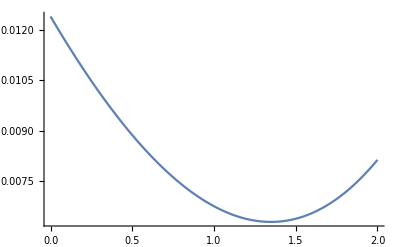

```mathematica
Plot[ϕ[α, x[[2]],p],{α,0,2}]
```

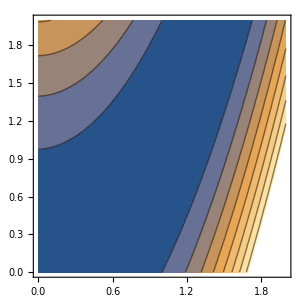

```mathematica
ContourPlot[f[x,y],{x,0,2},{y,0,2}]
```

```mathematica
Clear[x0]
```

```mathematica
f[{x0,x1}]//FullSimplify
```

(-1+x0)^2+20 (x0^2-x1)^2

```mathematica
D[f[{x0,x1}],x1,x0]//FullSimplify
```

-80 x0

```mathematica
D[f[{x0,x1}],x0,x1]//FullSimplify
```

-80 x0

```mathematica
D[f[{x1,x2}],{x1,1}]
```

-2 (1-x1)-80 x1 (-x1^2+x2)

```mathematica
gradf[{1,1}]
```

{0,0}

```mathematica
gradf[{x0,x1}]
```

{-2 (1-x0)-80 x0 (-x0^2+x1),40 (-x0^2+x1)}

```mathematica
Minimize[f[{x0,x1}],{x0,x1}]
```

{0,{x0→1,x1→1}}

```mathematica
f[{1,1}]
```

0

```mathematica
Plot3D[f[{x0,x1}],{x0,.99,1.01},{x1,.99,1.01}]
```

-Graphics3D-

```mathematica
f[{x0,x1}]
```

(1-x0)^2+20 (-x0^2+x1)^2

```mathematica
phid[α,{x0,x1},{p0,p1}]
```

40 (p1-2 p0 (x0+p0 α)) (x1+p1 α-(x0+p0 α)^2)

```mathematica
D[f[{x0,x1} + α*{p0,p1}],{α,2}]//FullSimplify
```

40 p1^2+2 p0 (-80 p1 x0+p0 (1-40 x1-120 p1 α+120 (x0+p0 α)^2))

```mathematica
Clear[x,p]
```

```mathematica
D[ϕ[α,x,p],α]
```

40 p (-x^2+p α)

```mathematica
ϕ[α,x,p]
```

(1-x)^2+20 (-x^2+p α)^2

```mathematica
f[(x + α*p)]
```

(1-x)^2+20 (-x^2+p α)^2

```mathematica
f[x]
```

(1-x⟦1⟧)^2+20 (-x⟦1⟧^2+x⟦2⟧)^2

```mathematica
(x + α*p)[[2]]
```

p α